# Discrete Power-law fitter

## Model extensions

For the bounded model in the range [x_min, x_max]

```mathematica
Solve[∑_(x=xMin)^xMax C[α,x] x^-α == 1,C[α,x]]
```

{{C[α,x]→1/(-HurwitzZeta[α,1+xMax]+HurwitzZeta[α,xMin])}}

That is:

```mathematica
p[x_,α_,xMin_,xMax_]:=x^-α/(HurwitzZeta[α,xMin]-HurwitzZeta[α,1+xMax]);
```

The form of the CDF therefore is:

```mathematica
∑_(xp=x)^xMax p[xp,α,xMin,xMax]
```

(HurwitzZeta[α,x]-HurwitzZeta[α,1+xMax])/(-Zeta[α,1+xMax]+Zeta[α,xMin])

```mathematica
P[x_,α_,xMin_,xMax_]:=(HurwitzZeta[α,x]-HurwitzZeta[α,1+xMax])/(HurwitzZeta[α,xMin]-HurwitzZeta[α,1+xMax]);
```

Thus, the log-likelihood can be expressed as:

```mathematica
FullSimplify@PowerExpand@Log[Product[x^-α/(HurwitzZeta[α,xMin]-HurwitzZeta[α,1+xMax]),{x,{x1,x2,x3,x4,x5}}]]
```

-α (Log[x1]+Log[x2]+Log[x3]+Log[x4]+Log[x5])-5 Log[-HurwitzZeta[α,1+xMax]+HurwitzZeta[α,xMin]]

That is, for an arbitrary sized sample:

```mathematica
L = - n * Log[HurwitzZeta[alpha,xMin]-HurwitzZeta[α,1+xMax]]-α ∑_(i=1)^n Log[x[[i]]]
```

## Implementation

```mathematica
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]]
```

```mathematica
DiscretePowerLawDistributionPDF[α_,xMin_,x_]:=x^-α/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionPDF[α_,xMin_,xMax_,x_]:=x^-α/(HurwitzZeta[α,xMin]-HurwitzZeta[α,1+xMax]);;
DiscretePowerLawDistributionCDF[α_,xMin_,x_]:=HurwitzZeta[α,x]/HurwitzZeta[α,xMin];
DiscretePowerLawDistributionCDF[α_,xMin_,xMax_,x_]:=(HurwitzZeta[α,x]-HurwitzZeta[α,1+xMax])/(Zeta[α,xMin]-Zeta[α,1+xMax]);
EmpiricalCDF[data_,x_]:= N[1-CDF[EmpiricalDistribution[data],x-1]];
GeneratePowerlawSampleData[α_,xMin_,xMax_,sampleSize_ :1000]:=Block[{dist},
dist = ProbabilityDistribution[DiscretePowerLawDistributionPDF[α,xMin,xMax,x],{x,xMin,xMax,1}];

RandomVariate[dist,sampleSize]

];
```

```mathematica
HistogramPoints[data_]:=Map[{#,N[Count[data,#]/Length[data]]}&,Sort[DeleteDuplicates[data]]];
HistogramPointPlots[data_List,opts: OptionsPattern[]]:=Block[{pltData = HistogramPoints[data]},
ListPlot[
pltData,
Joined->False,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
PlotStyle->{PointSize[Large],ColorData["Legacy"]["IndianRed"]},
ImageSize->500,
PlotMarkers->None,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FilterRules[{opts},Options[ListPlot]]
]
];
```

```mathematica
SelectTail[data_,xMin_]:=Select[data,#>=xMin&];
SelectTruncatedTail[data_,xMin_,xMax_]:=Select[data,xMin<=#<=xMax&];
SelectBulk[data_,xMin_]:=Select[data,#<xMin&];

CalculateLogLikelihood[data_,alpha_, xMin_]:=Block[{tail,n},
tail = SelectTail[data,xMin];
n = Length[tail];
N[- n * Log[HurwitzZeta[alpha,xMin]]-alpha ∑_(i=1)^n Log[tail[[i]]]]
];
CalculateLogLikelihood[data_,alpha_, xMin_,xMax_]:=Block[{tail,n},
tail = SelectTruncatedTail[data,xMin,xMax];
n = Length[tail];
N[- n * Log[HurwitzZeta[alpha,xMin]-HurwitzZeta[alpha,1+xMax]]-alpha ∑_(i=1)^n Log[tail[[i]]]]
];
EstimateαPrecise[data_,xMin_]:=Block[{tail,L},
tail = SelectTail[data,xMin];
L = Table[{α,CalculateLogLikelihood[tail,α, xMin]},{α,1.5,3.51,0.01}];
<|"Alpha"->MaximalBy[L,Last][[1,1]], "xMin"->xMin|>
];
EstimateαPrecise[data_,xMin_,xMax_]:=Block[{tail,L},
tail = SelectTruncatedTail[data,xMin,xMax];
L = Table[{α,CalculateLogLikelihood[tail,α, xMin,xMax]},{α,1.5,3.51,0.01}];
<|"Alpha"->MaximalBy[L,Last][[1,1]], "xMin"->xMin,"xMax"->xMax|>
];
```

```mathematica
KSStatistic[data_,xMin_Integer]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,xMin];
αEstimator = EstimateαPrecise[data,xMin]["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,xMin,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,xMin_Integer,xMax_Integer]:=Block[{tail,αEstimator,diff},
tail = SelectTruncatedTail[data,xMin,xMax];
αEstimator = EstimateαPrecise[data,xMin,xMax]["Alpha"];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,xMin,xMax,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,xMin_Integer,xMax_Integer,alpha_]:=Block[{tail,diff},
tail = SelectTruncatedTail[data,xMin,xMax];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[alpha,xMin,xMax,x]],{x,xMin,xMax}];
Max[diff]
];
KSStatistic[data_,model_Association]:=Block[{xMax,tail,αEstimator,diff},
tail = SelectTail[data,model["xMin"]];
αEstimator = model["Alpha"];
xMax = Max[data];
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,model["xMin"],x]],{x,model["xMin"],xMax}];
Max[diff]
];
KSStatistic[data_]:=KSStatistic[data,EstimateαAndXMin[data]];
EstimateαAndXMin[data_]:=Block[{minElement,maxElement,xMin},
{minElement,maxElement} = MinMax[data];
xMin = MinimalBy[Table[{x,KSStatistic[data,x]},{x,minElement,maxElement-1}],Last][[1,1]];
EstimateαPrecise[data,xMin]
];
EstimateAll[data_,smallestInterval_ : 20]:=Block[{minElement,maxElement,xMin,xMax},
{minElement,maxElement} = MinMax[data];
xMin = MinimalBy[ProgressTable[{x,KSStatistic[data,x]},{x,minElement,maxElement-1},"Label"->"Searching for x_min"],Last][[1,1]];
xMax = MinimalBy[ProgressTable[{x,KSStatistic[data,xMin,x]},{x,xMin+smallestInterval,maxElement},"Label"->"Searching for x_max"],Last][[1,1]];
EstimateαPrecise[data,xMin,xMax]
];
GenerateBootstrapReplica[data_,model_]:=Block[{n,bulk, tail,tailProbability,tailReplica,bulkReplica},
n = Length[data];
bulk = SelectBulk[data,model["xMin"]];
tail = SelectTail[data,model["xMin"]];
tailProbability = 1.0 - Length[bulk]/n;
tailReplica = GeneratePowerlawSampleData[model["Alpha"],model["xMin"],Max[data],Floor[n*tailProbability]];
bulkReplica = RandomSample[bulk,n-Floor[n*tailProbability]];
RandomSample[Join[tailReplica, bulkReplica]]
];
GenerateFixedMinBootstrapReplica[model_,xMax_,n_]:=GeneratePowerlawSampleData[model["Alpha"],model["xMin"],xMax,n];
CalculateGOF[data_,replicas_:2000]:=Block[{model,ksOfData,syntheticKsValues,pValue},
model = EstimateαAndXMin[data];
ksOfData = KSStatistic[data,model];
syntheticKsValues = ProgressTable[KSStatistic[GenerateBootstrapReplica[data,model]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->model["Alpha"],"xMin"->model["xMin"],"p-value"->pValue|>
];
CalculateFixedMinGOF[data_,xMin_,replicas_:2000]:=Block[{fixedMinModel,ksOfData,n,syntheticKsValues,pValue},
fixedMinModel = EstimateαPrecise[data,xMin];
ksOfData = KSStatistic[data,xMin];
n = Length[SelectTail[data,xMin]];
syntheticKsValues = ProgressTable[KSStatistic[GenerateFixedMinBootstrapReplica[fixedMinModel,Max[data],n]],replicas];
pValue = N[Count[syntheticKsValues,x_ /; x>ksOfData]/Length[syntheticKsValues]];
<|"Alpha"->fixedMinModel["Alpha"],"xMin"->fixedMinModel["xMin"],"p-value"->pValue|>
];
```

```mathematica
sample = GeneratePowerlawSampleData[2.5,1,100,2000];
```

```mathematica
EstimateAll[sample]
```

<|Alpha→1.71,xMin→1,xMax→46|>

```mathematica
EstimateαPrecise[sample,1,21]
```

<|Alpha→1.69,xMin→1,xMax→21|>

```mathematica
CalculateLogLikelihood[sample,1.5, 1,21]
```

-4494.48

```mathematica
KSStatistic[sample,1,21]
```

0.0291149

```mathematica
tail = SelectTruncatedTail[sample,1,21];
αEstimator = EstimateαPrecise[sample,1,21]["Alpha"]
```

1.69

```mathematica
diff = Table[Abs[EmpiricalCDF[tail,x]-DiscretePowerLawDistributionCDF[αEstimator,1,21,x]],{x,1,21}];
Max[diff]
```

```mathematica
ProgressTable[{x,KSStatistic[sample,1,x]},{x,1+20,93},"Label"->"Searching for x_max"]
```

{{21,0.0291149},{22,0.0290776},{23,0.0295826},{24,0.0299886},{25,0.0274115},{26,0.0278445},{27,0.0277787},{28,0.0278668},{29,0.0270485},{30,0.026611},{31,0.0299939},{32,0.0266644},{33,0.0271574},{34,0.027614},{35,0.0243452},{36,0.0243055},{37,0.0273302},{38,0.0276686},{39,0.0244502},{40,0.02473},{41,0.0247811},{42,0.0248132},{43,0.0250347},{44,0.0248253},{45,0.0241888},{46,0.0239519},{47,0.0271113},{48,0.0266547},{49,0.0263912},{50,0.0261169},{51,0.0260353},{52,0.0294176},{53,0.0291221},{54,0.0286167},{55,0.0283049},{56,0.0283863},{57,0.0284592},{58,0.031466},{59,0.0315305},{60,0.0311893},{61,0.0304455},{62,0.0340809},{63,0.0303291},{64,0.0339649},{65,0.0336024},{66,0.0332352},{67,0.0330598},{68,0.0326836},{69,0.0365467},{70,0.0361677},{71,0.0361744},{72,0.0361764},{73,0.0352031},{74,0.0350035},{75,0.0348002},{76,0.0349796},{77,0.0347687},{78,0.0384753},{79,0.0380707},{80,0.0382394},{81,0.0382126},{82,0.0381825},{83,0.0377661},{84,0.03773},{85,0.037691},{86,0.0374582},{87,0.0376044},{88,0.0375571},{89,0.0376978},{90,0.0378359},{91,0.0375902},{92,0.0375329},{93,0.0374732}}

```mathematica
ksValues = Table[{xMin,xMax,KSStatistic[sample,xMin,xMax]},{xMin,1,50},{xMax,xMin+1,50}];
```

```mathematica
ksValues = ProgressTable[{xMin,KSStatistic[sample,xMin]},{xMin,1,50}];
```

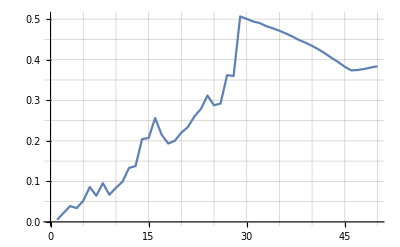

```mathematica
ListLinePlot[ksValues,PlotRange->All,GridLines->All]
```

```mathematica
ksValues = ProgressTable[{xMax,KSStatistic[sample,1,xMax]},{xMax,2,100}];
```

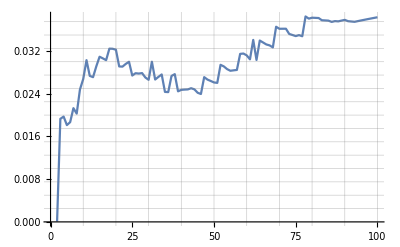

```mathematica
ListLinePlot[ksValues,PlotRange->All,GridLines->All]
```

```mathematica
model = <|"Alpha"->1.71,"xMin"->1,"xMax"->46|>;
```

```mathematica
cutSample=SelectTruncatedTail[sample,1,46];
```

0.0239519

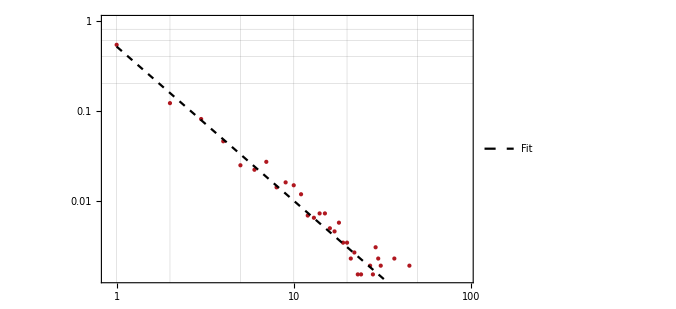

```mathematica
KSStatistic[cutSample,1,46,1.71]
Show[
HistogramPointPlots[cutSample,
ScalingFunctions->{"Log","Log"},
PlotRange->{{0.9,Max[sample]+1},{0,1}}
],
Plot[DiscretePowerLawDistributionPDF[1.71,1,46,x],{x,1,46},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"Fit"},
PlotStyle->{Dashed,Black}
]
]
```

0.0200949

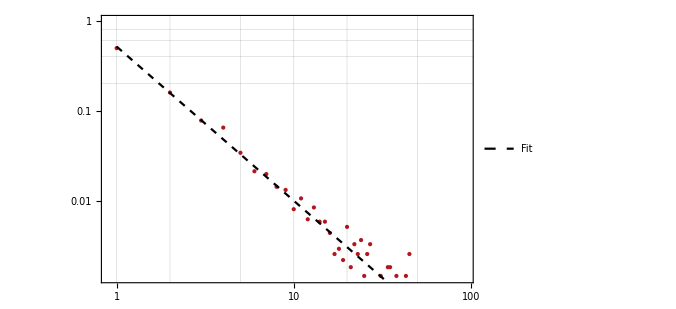

```mathematica
synthSample = GeneratePowerlawSampleData[1.71,1,46,Length[sample]];
KSStatistic[synthSample,1,46,1.71]
Show[
HistogramPointPlots[synthSample,
ScalingFunctions->{"Log","Log"},
PlotRange->{{0.9,Max[sample]+1},{0,1}}
],
Plot[DiscretePowerLawDistributionPDF[1.71,1,46,x],{x,1,46},
ScalingFunctions->{"Log","Log"},
PlotLegends->{"Fit"},
PlotStyle->{Dashed,Black}
]
]
```